```mathematica
(*SetOptions[ListPlot,{PlotRange->{ 2 10^-4,10^-3}}];*)
```

```mathematica
path="/home/kareem/hep/SSP/Output/";
Get[path<>"plot.m"]
st[x_]:=ToString[x];
ex[x_]:=ToExpression[x];
dat1={"vRInput","lam1INPUT","lam2INPUT","lam3INPUT","lam4INPUT","rho1INPUT","alp1INPUT","alp2INPUT","alp3INPUT","alp4INPUT","vHdINPUT","vHuINPUT","TanBeta","hh_2","HB Result (1: allowed, 0: excluded, -1: unphysical)","HS total Chi^2","xsection"};
dat2={"dh_2","mh_2"};
prcs={"pphhaabb","ppzz4l"};
prcs1={"pphhaabb"};
prcs2={"ppzz4l"};
prcs=prcs;
Do[ex[prcs[[i]]<>dat1[[j]]]=Import[path<>prcs[[i]]<>"_"<>dat1[[j]]<>".dat"];,{i,Length[prcs]},{j,Length[dat1]}];
Do[ex["l1"<>prcs[[i]]<>dat1[[j]]]=Length[ex[prcs[[i]]<>dat1[[j]]]];,{i,Length[prcs]},{j,Length[dat1]}];
Do[ex["l2"<>prcs[[i]]<>dat1[[j]]]=Length[ex[prcs[[i]]<>dat1[[j]]][[1]]];,{i,Length[prcs]},{j,Length[dat1]}];
Do[Export[path<>prcs[[j]]<>"_dh_2.dat",Table[ex[prcs[[j]]<>"hh_2"][[2i]],{i,Ceiling[Length[ex[prcs[[j]]<>"hh_2"]]/2]}]]&&Export[path<>prcs[[j]]<>"_mh_2.dat",Table[ex[prcs[[j]]<>"hh_2"][[2i-1]],{i,Ceiling[Length[ex[prcs[[j]]<>"hh_2"]]/2]}]];,{j,Length[prcs]}];
```

Get::noopen: Cannot open "/home/kareem/hep/SSP/Output/plot.m".

$Failed

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Export::nodir: Directory "/home/kareem/hep/SSP/Output/" does not exist.

OpenWrite::noopen: Cannot open "/home/kareem/hep/SSP/Output/pphhaabb_dh_2.dat".

Export::nodir: Directory "/home/kareem/hep/SSP/Output/" does not exist.

OpenWrite::noopen: Cannot open "/home/kareem/hep/SSP/Output/pphhaabb_mh_2.dat".

Export::nodir: Directory "/home/kareem/hep/SSP/Output/" does not exist.

General::stop: Further output of Export :: nodir will be suppressed during this calculation.

OpenWrite::noopen: Cannot open "/home/kareem/hep/SSP/Output/ppzz4l_dh_2.dat".

General::stop: Further output of OpenWrite :: noopen will be suppressed during this calculation.

```mathematica
Do[ex[prcs[[i]]<>dat2[[j]]]=Import[path<>prcs[[i]]<>"_"<>dat2[[j]]<>".dat"];,{i,Length[prcs]},{j,Length[dat2]}];
Do[ex["l1"<>prcs[[i]]<>dat2[[j]]]=Length[ex[prcs[[i]]<>dat2[[j]]]];,{i,Length[prcs]},{j,Length[dat2]}];
Do[ex["l2"<>prcs[[i]]<>dat2[[j]]]=Length[ex[prcs[[i]]<>dat2[[j]]][[1]]];,{i,Length[prcs]},{j,Length[dat2]}];
SetOptions[ListPlot,PlotRange->All];
```

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
lstplt[i1_,j1_,i2_,j2_]:=ListPlot[Table[{ex[prcs[[i1]]<>dat1[[j1]]][[k,Length[ex[prcs[[i1]]<>dat1[[j1]]][[1]]]]],ex[prcs[[i2]]<>dat1[[j2]]][[k,Length[ex[prcs[[i2]]<>dat1[[j2]]][[1]]]]]},{k,Length[ex[prcs[[i1]]<>dat1[[j1]]]]}],FrameLabel->{prcs[[i1]]<>dat1[[j1]],prcs[[i2]]<>dat1[[j2]]}]
(*Do[Print[lstplt[i1,j1,i2,j2]],{i1,Length[prcs]},{j1,Length[dat1]},{i2,Length[prcs]},{j2,j1+1,2+0Length[dat1]}]*)
```

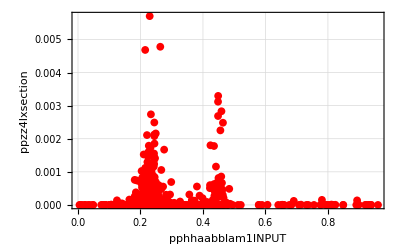

```mathematica
lstplt[1,2,2,Length[dat1]]
```

```mathematica
lstplt1[i1_,j1_,i2_,j2_]:=ListPlot[Table[{ex[prcs[[i2]]<>dat2[[j2]]][[k,Length[ex[prcs[[i2]]<>dat2[[j2]]][[1]]]]],ex[prcs[[i1]]<>dat1[[j1]]][[k,Length[ex[prcs[[i1]]<>dat1[[j1]]][[1]]]]]},{k,Length[ex[prcs[[i1]]<>dat1[[j1]]]]}],FrameLabel->{prcs[[i2]]<>dat2[[j2]],prcs[[i1]]<>dat1[[j1]]}]
(*Do[Print[lstplt[i1,j1,i2,j2]],{i1,Length[prcs]},{j1,Length[dat1]},{i2,Length[prcs]},{j2,j1+1,2+0Length[dat1]}]*)
```

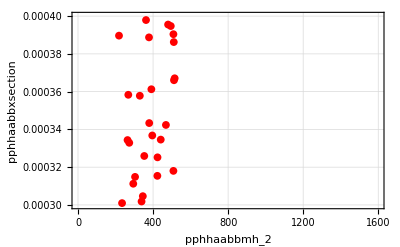

```mathematica
lstplt1[1,Length[dat1],1,Length[dat2]]
```

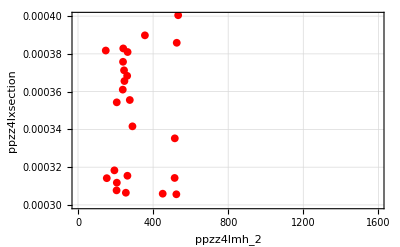

```mathematica
lstplt1[2,Length[dat1],2,Length[dat2]]
```

# ppzz4l

```mathematica
ppzz4ltxsection=ex[prcs[[2]]<>dat1[[Length[dat1]]]];
l1ppzz4lxsection=ex["l1"<>prcs[[2]]<>dat1[[Length[dat1]]]];
l2ppzz4lxsection=ex["l2"<>prcs[[2]]<>dat1[[Length[dat1]]]];
ppzz4ltxsection1=Table[ppzz4ltxsection[[i,l2ppzz4lxsection]],{i,l1ppzz4lxsection}];
Length[ppzz4ltxsection1]
```

3215

```mathematica
ppzz4lxsectionmaxpos=Ordering[ppzz4ltxsection1,-1]
ppzz4lxsectionmax=Extract[ppzz4ltxsection1,ppzz4lxsectionmaxpos]
(*Extract[thh2,ppzz4lxsectionmaxpos]*)
ppzz4ltxsection[[ppzz4lxsectionmaxpos]]
```

{1970}

0.00570343

{{19_109,0.00570343}}

```mathematica
thh2mdppzz4l=Import[path<>"ppzz4l_hh_2.dat"];
thh2ppzz4l=Table[thh2mdppzz4l[[2i-1]],{i,Ceiling[Length[thh2mdppzz4l]/2]}];
thh2dppzz4l=Table[thh2mdppzz4l[[2i]],{i,0,Ceiling[Length[thh2mdppzz4l]/2]}];
l1hh2ppzz4l=Length[thh2ppzz4l];
l2hh2ppzz4l=Length[thh2ppzz4l[[1]]];
thh2ppzz4l[[ppzz4lxsectionmaxpos]]
```

{{19_109,35,188.979}}

```mathematica
ppzz4lHS1=ex[prcs[[2]]<>dat1[[Length[dat1]-1]]];
l1ppzz4lHS1=ex["l1"<>prcs[[1]]<>dat1[[Length[dat1]-1]]];
l2ppzz4lHS1=ex["l2"<>prcs[[1]]<>dat1[[Length[dat1]-1]]];
ppzz4lHS=Table[ppzz4lHS1[[i,l2ppzz4lHS1]],{i,l1ppzz4lHS1}];
ppzz4lHS2=Ordering[ppzz4lHS];
Length[ppzz4lHS]
```

3214

```mathematica
ppzz4lHB1=ex[prcs[[2]]<>dat1[[Length[dat1]-2]]];
l1ppzz4lHB1=ex["l1"<>prcs[[1]]<>dat1[[Length[dat1]-2]]];
l2ppzz4lHB1=ex["l2"<>prcs[[1]]<>dat1[[Length[dat1]-2]]];
ppzz4lHB=Table[ppzz4lHB1[[i,l2ppzz4lHB1]],{i,l1ppzz4lHB1}];
ppzz4lHB2=Ordering[ppzz4lHB];
Length[ppzz4lHB]
```

3214

```mathematica
Ordering[ppzz4ltxsection1];
ptppzz4l[i_,j_]:={Ordering[ppzz4ltxsection1,-i][[j]],300000Extract[ppzz4ltxsection1,Ordering[ppzz4ltxsection1,-i][[j]]],
ppzz4ltxsection[[Ordering[ppzz4ltxsection1,-i][[j]]]],Extract[thh2ppzz4l,Ordering[ppzz4ltxsection1,-i][[j]]],ppzz4lHS1[[Ordering[ppzz4ltxsection1,-i][[j]]]],ppzz4lHB1[[Ordering[ppzz4ltxsection1,-i][[j]]]]};
Do[Print[ptppzz4l[i,1]],{i,3214}]
```

```mathematica
ptppzz4l[1,1]
```

# pphhaabb

```mathematica
pphhaabbtxsection=ex[prcs[[1]]<>dat1[[Length[dat1]]]];
l1pphhaabbxsection=ex["l1"<>prcs[[1]]<>dat1[[Length[dat1]]]];
l2pphhaabbxsection=ex["l2"<>prcs[[1]]<>dat1[[Length[dat1]]]];
pphhaabbtxsection1=Table[pphhaabbtxsection[[i,l2pphhaabbxsection]],{i,l1pphhaabbxsection}];
pphhaabbtxsection2=Ordering[pphhaabbtxsection1];
Length[pphhaabbtxsection1]
```

3214

```mathematica
pphhaabbxsectionmaxpos=Ordering[pphhaabbtxsection1,-1]
pphhaabbxsectionmax=Extract[pphhaabbtxsection1,pphhaabbxsectionmaxpos]
(*Extract[thh2,pphhaabbxsectionmaxpos]*)
pphhaabbtxsection[[pphhaabbxsectionmaxpos]]
```

{3196}

0.0076678

{{28_97,0.0076678}}

```mathematica
thh2mdpphhaabb=Import[path<>"pphhaabb_hh_2.dat"];
thh2pphhaabb=Table[thh2mdpphhaabb[[2i-1]],{i,Ceiling[Length[thh2mdpphhaabb]/2]}];
thh2dpphhaabb=Table[thh2mdpphhaabb[[2i]],{i,Ceiling[Length[thh2mdpphhaabb]/2]}];
l1hh2pphhaabb=Length[thh2pphhaabb];
l2hh2pphhaabb=Length[thh2pphhaabb[[1]]];
thh2pphhaabb[[pphhaabbxsectionmaxpos]]
```

{{28_97,35,289.001}}

```mathematica
pphhaabbHS1=ex[prcs[[1]]<>dat1[[Length[dat1]-1]]];
l1pphhaabbHS1=ex["l1"<>prcs[[1]]<>dat1[[Length[dat1]-1]]];
l2pphhaabbHS1=ex["l2"<>prcs[[1]]<>dat1[[Length[dat1]-1]]];
pphhaabbHS=Table[pphhaabbHS1[[i,l2pphhaabbHS1]],{i,l1pphhaabbHS1}];
pphhaabbHS2=Ordering[pphhaabbHS];
Length[pphhaabbHS]
```

3214

```mathematica
pphhaabbHB1=ex[prcs[[1]]<>dat1[[Length[dat1]-2]]];
l1pphhaabbHB1=ex["l1"<>prcs[[1]]<>dat1[[Length[dat1]-2]]];
l2pphhaabbHB1=ex["l2"<>prcs[[1]]<>dat1[[Length[dat1]-2]]];
pphhaabbHB=Table[pphhaabbHB1[[i,3]],{i,l1pphhaabbHB1}];
pphhaabbHB2=Ordering[pphhaabbHB];
Length[pphhaabbHB]
```

3214

```mathematica
0.0076678*289.000529
```

2.216

```mathematica
0.0043981*308.56371
```

1.35709

```mathematica
(*Table[ex[prcs[[1]]<>"hh_2"][[2i-1]],{i,Ceiling[Length[ex[prcs[[1]]<>"hh_2"]]/2]}]*)
```

```mathematica
Ordering[pphhaabbtxsection1];
ptpphhaabb[i_,j_]:={Ordering[pphhaabbtxsection1,-i][[j]],300000Extract[pphhaabbtxsection1,Ordering[pphhaabbtxsection1,-i][[j]]],
pphhaabbtxsection[[Ordering[pphhaabbtxsection1,-i][[j]]]],Extract[thh2pphhaabb,Ordering[pphhaabbtxsection1,-i][[j]]],pphhaabbHS1[[Ordering[pphhaabbtxsection1,-i][[j]]]],pphhaabbHB1[[Ordering[pphhaabbtxsection1,-i][[j]]]]};
Do[Print[ptpphhaabb[i,1]],{i,1}]
```

{3196,2300.34,{28_97,0.0076678},{28_97,35,289.001},{28_97,8,169.148},{28_97,6,1}}

```mathematica
(*ListPlot[Table[{i,Import[path<>"pphhaabb_xsection.dat"][[i,l2pphhaabbxsection]]},{i,l1pphhaabbxsection}]]*)
```

```mathematica
(*data=Table[{thh2[[i, 3]],pphhaabbtxsection[[i, l2pphhaabbxsection]],tchi2[[i, 3]]}, {i,  l1pphhaabbxsection}];*)
```

```mathematica
(*sgnplt=ListPlot[List/@data[[All,{1,2}]],PlotStyle->({PointSize[0.01],ColorData["Rainbow"][#1]}&/@Rescale[data[[All,3]],{70,150}]),PlotRange->Full,AspectRatio->1,Frame->True,Axes->None]*)
```

```mathematica
(*Clear[colorbar]
colorbar[{min_,max_},colorFunction_: Automatic,divs_: 150]:=DensityPlot[y,{x,0,0.1},{y,min,max},AspectRatio->10,PlotRangePadding->0,PlotPoints->{2,divs},MaxRecursion->0,FrameTicks->{None,Automatic,None,None},ColorFunction->colorFunction];
With[{opts={ImageSize->{Automatic,300},ImagePadding->20},cf="Rainbow"},Row[{ListPlot[List/@data[[All,{1,2}]],PlotStyle->({PointSize[0.01],ColorData["Rainbow"][#1]}&/@Rescale[data[[All,3]],{70,150}]),PlotRange->Full,AspectRatio->1,Frame->True,Axes->None,FrameTicks->True,opts],Show[colorbar[{70,150},cf],opts]}]]*)
```

```mathematica
(*Clear[colorbar]
colorbar[{min_,max_},colorFunction_: Automatic,divs_: 150]:=DensityPlot[y,{x,0,0.1},{y,min,max},AspectRatio->10,PlotRangePadding->0,PlotPoints->{2,divs},MaxRecursion->0,Frame->True,FrameLabel->{{None,"χ^2"},{None,None}},LabelStyle->Directive[FontFamily->"Helvetica",14,Bold],FrameTicks->{{None,All},{None,None}},FrameTicksStyle->Directive[FontFamily->"Helvetica",10,Plain],ColorFunction->colorFunction];

With[{opts={ImageSize->{Automatic,300}},cf="Rainbow"},Row[{ListPlot[List/@data[[All,{1,2}]],PlotStyle->({PointSize[0.01],ColorData[cf][#1]}&/@Rescale[data[[All,3]],{70,150}]),PlotRange->{10^-4,2 10^-4},AspectRatio->1,Frame->True,Axes->None,FrameTicks->True,LabelStyle->Directive[FontFamily->"Helvetica",10],ImagePadding->{{40,10},{20,20}},opts],Show[colorbar[{70,150},cf],ImagePadding->{{10,40},{20,20}},opts]}]]*)
```

# ppzz4lt-pphhaabb

Part::partw: Part 8049 of {{"51_0", 0.000240569}, {"51_1", 0.000155123}, {"51_2", 0.000111308}, {"51_3", 0.000206413}, {"51_4", 0.00011756}, {"51_5", 0.000214709}, {"51_6", 0.000196488}, {"51_7", 0.000179575}, {"51_8", 0.000216364}, « 34 », {"51_43", 0.0000886897}, {"51_44", 0.000152958}, {"51_45", 0.000192383}, {"51_46", 0.000152701}, {"51_47", 0.000121481}, {"51_48", 0.000169586}, {"51_49", 0.0000373379}, « 7998 »} does not exist.

Part::partw: Part 8050 of {{"51_0", 0.000240569}, {"51_1", 0.000155123}, {"51_2", 0.000111308}, {"51_3", 0.000206413}, {"51_4", 0.00011756}, {"51_5", 0.000214709}, {"51_6", 0.000196488}, {"51_7", 0.000179575}, {"51_8", 0.000216364}, « 34 », {"51_43", 0.0000886897}, {"51_44", 0.000152958}, {"51_45", 0.000192383}, {"51_46", 0.000152701}, {"51_47", 0.000121481}, {"51_48", 0.000169586}, {"51_49", 0.0000373379}, « 7998 »} does not exist.

Part::partw: Part 8051 of {{"51_0", 0.000240569}, {"51_1", 0.000155123}, {"51_2", 0.000111308}, {"51_3", 0.000206413}, {"51_4", 0.00011756}, {"51_5", 0.000214709}, {"51_6", 0.000196488}, {"51_7", 0.000179575}, {"51_8", 0.000216364}, « 34 », {"51_43", 0.0000886897}, {"51_44", 0.000152958}, {"51_45", 0.000192383}, {"51_46", 0.000152701}, {"51_47", 0.000121481}, {"51_48", 0.000169586}, {"51_49", 0.0000373379}, « 7998 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

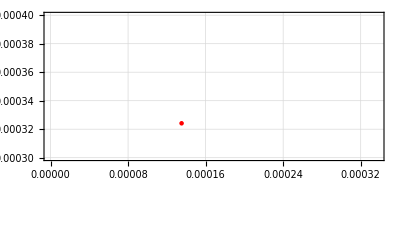

```mathematica
lstplt[1,Length[dat1],2,Length[dat1]]
```

```mathematica
(*i=2;j,k=1; {g1,gBy,gyB,g2,gB,vu,vd,vη,vηbar,ZHi1,ZHi2,ZHi3,ZHi4}*)
ghihjhk=I/4(ZHi1 ((g1^2+gyB^2+g2^2)ZHj2(vd ZHk2+vu ZHk1)-2(g1 gBy+gyB gB)(ZHj3(vd ZHk3+vη ZHk1)-ZHj4(vηbar ZHk1+vd ZHk4))+ZHj1(-2(g1 gBy+gyB gB)(-vηbar ZHk4+vη ZHk3)+(g1^2+gyB^2+g2^2)(-3vd ZHk1+vu ZHk2)))+ZHi2 ((g1^2+gyB^2+g2^2)ZHj1(vd ZHk2+vu ZHk1)+2(g1 gBy+gyB gB)(ZHj3(vu ZHk3+vη ZHk2)-ZHj4(vηbar ZHk2+vu ZHk4))+ZHj2(2(g1 gBy+gyB gB)(-vηbar ZHk4+vη ZHk3)+(g1^2+gyB^2+g2^2)(-3vu ZHk2+vd ZHk1)))-2ZHi3 (-(g1 gBy+gyB gB)ZHj2(vη ZHk2+vu ZHk3)+(g1 gBy+gyB gB)ZHj1(vd ZHk3+vη ZHk1)-2(gB^2+gBy^2)ZHj4(vηbar ZHk3+vη ZHk4)+2ZHj3((gB^2+gBy^2)(3vη ZHk3-vηbar ZHk4)+(g1 gBy+gyB gB)(vd ZHk1-vu ZHk2)))+2ZHi4 (-(g1 gBy+gyB gB)ZHj2(vηbar ZHk2+vu ZHk4)+(g1 gBy+gyB gB)ZHj1(vηbar ZHk1+vd ZHk4)+2(gB^2+gBy^2)ZHj3(vηbar ZHk3+vη ZHk4)+2ZHj4((gB^2+gBy^2)(-3vη ZHk4-vηbar ZHk3)+(g1 gBy+gyB gB)(vd ZHk1-vu ZHk2))));
ghiZZ=I/2((g1 cwp sw+g2 cw cwp-gyB swp)^2(vd ZHi1 +vu ZHi2) +4(gB swp-gyB cwp sw)^2(vηbar ZHi3 +vηbar ZHi4) );
```